# Correlation Sampling (Displacement) - Simulation

## Last Updated: 2025/07/18

```mathematica
(*Quit[];*)
```

```mathematica
(*Clear["Global`*"];*)
```

# General

## Values

## ARTIQ Conversions

```mathematica
(*convert 32-bit frequency tuning word (FTW) to MHz (assuming 0xFFFFFFFF is 1 GHz)*)
ftwToFrequencyMHz=(1.*^-6)*(1.*^9)/(Interpreter["HexInteger"]["FFFFFFFF"]);
```

```mathematica
(*convert 32-bit frequency tuning word (FTW) to MHz (assuming 0xFFFFFFFF is 1 GHz)*)
asfToAmplitudePCT=(1.*^2)*1./(Interpreter["HexInteger"]["3FFF"]);
```

## Fundamental

```mathematica
(*natural*)
ℏ=1.0545718*^-34;
c=2.99792458*^8;
```

```mathematica
(*statistical mechanics*)
kb=1.38064852*^-23;
```

```mathematica
(*electron units*)
me=9.10938356*^-31;
qe=1.60217662*^-19;
```

```mathematica
(*electromagnetism*)
ϵ0 = 8.8541878128*^-12;
μ0=π*4.*^-7;
```

```mathematica
(*atomic*)
amu=1.66053904*^-27;
```

## Derived

```mathematica
(*qe^2/(4 Subscript[πϵ, 0])*)
ke2=2.30707751*^-28;
```

```mathematica
(*fine structure constant*)
αfs=ke2/(ℏ*c);
```

```mathematica
(*bohr radius*)
a0=ℏ^2/(me*ke2);
```

```mathematica
(*bohr magneton*)
μB=(qe*ℏ)/(2*me);
```

```mathematica
(*debye*)
debye=(1.*^-21)/c;
```

## Units

```mathematica
(*frequency*)
{hz,khz,mhz,ghz}={1.,10.^3,10.^6,10.^9};
{whz,wkhz,wmhz,wghz}=2.π*{1.,10.^3,10.^6,10.^9};
```

```mathematica
(*time*)
{ns,μs,ms}={10.^-9,10.^-6,10.^-3};
```

```mathematica
(*distance*)
{nm,μm,mm}={10.^-9,10.^-6,10.^-3};
```

## Plotting

```mathematica
(*set plot options*)
SetOptions[Plot,Frame-> True,FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
SetOptions[ListPlot,Frame-> True,FrameTicksStyle-> Directive[Black,15],Joined->False,Background->White,ImageSize->Large,GridLines->Automatic];
SetOptions[ListLinePlot,Frame-> True, FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic,GridLines->Automatic];
SetOptions[ListLogPlot,Frame-> True, FrameTicksStyle-> Directive[Black,15],Joined->True,Background->White,ImageSize->Large,GridLines->Automatic];SetOptions[ListLogLogPlot,Frame-> True, FrameTicksStyle-> Directive[Black,15],Joined->True,Background->White,ImageSize->Large,GridLines->Automatic];
SetOptions[Histogram,Frame-> True, FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
SetOptions[ComplexListPlot,Frame-> True,FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
```

```mathematica
(*set signal plot options*)
SetOptions[Histogram,Frame-> True, FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
SetOptions[ComplexListPlot,Frame-> True,FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
```

```mathematica
(*set 3d plot options*)
SetOptions[ListDensityPlot,Frame-> True, FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
SetOptions[ListPlot3D,Background->None,ImageSize->Large];
```

## Evaluations

```mathematica
(*scde2={
Off[General::munfl],
Off[FindRoot::lstol],
Off[FindFit::cvmit],
Off[FindFit::sszero],
Off[FindFit::nrjnum],
Off[NonlinearModelFit::cvmit],
Off[NonlinearModelFit::sszero],
Off[Power::infy],
Off[Infinity::indet],
Off[FittedModel::constr]
};*)
```

```mathematica
(*Evaluate[#]&/@scde2*)
```

```mathematica
(*scde={
General::munfl,
FindRoot::lstol,
FindFit::cvmit,
FindFit::sszero,
FindFit::nrjnum,
NonlinearModelFit::cvmit,
NonlinearModelFit::sszero,
Power::infy,
Infinity::indet,
FittedModel::constr
};*)
```

```mathematica
(*Off[#]&/@scde*)
```

```mathematica
(*turn upsetting things off*)
ParallelEvaluate[
Off[General::munfl];
Off[FindRoot::lstol];
Off[FindFit::cvmit];
Off[FindFit::sszero];
Off[FindFit::nrjnum];
Off[NonlinearModelFit::cvmit];
Off[NonlinearModelFit::sszero];
Off[Power::infy];
Off[Infinity::indet];
Off[FittedModel::constr];
Off[InterpolatingFunction::dmval];
Off[NIntegrate::slwcon];(*NIntegrate too slow convergence*)
];
Evaluate[
Off[General::munfl];
Off[FindRoot::lstol];
Off[FindFit::cvmit];
Off[FindFit::sszero];
Off[FindFit::nrjnum];
Off[NonlinearModelFit::cvmit];
Off[NonlinearModelFit::sszero];
Off[Power::infy];
Off[Infinity::indet];
Off[FittedModel::constr];
Off[InterpolatingFunction::dmval];
Off[NIntegrate::slwcon];(*NIntegrate too slow convergence*)
];
```

## Functions

# Create Displacement

## Generalized Polar Modulation Blocks

For discrete polar modulation (i.e. discrete blocks with variable amplitude Ω_n and phase ϕ_n), the resultant displacement is given by
	α_Total = ∑_(n=1)^N α_n, where
	α_n = τ Ω_n Sinc[δτ/2]  Exp[-ⅈδτ(n-1/2) +ⅈϕ_n]
		→ α_n = α_0 Sinc[δτ/2]  Exp[-ⅈδτ(n-1/2) +ⅈϕ_n]
		(since displacement magnitude is α_0=Ω_n τ)

```mathematica
(*
Create an expression for a displacement as a function of detuning (δ) and total time (T).
The returned expression gives only the FINAL displacement at the end, not the time evolution.
Assumes constituent blocks are evenly spaced.
*)
αBlock[δ_,αArr_List,ϕArr_List]:=Block[{T,t0},
With[
(*predeclare variables*)
{
τ=T/Length[αArr],
expArr=Exp[ⅈ*(ϕArr+(δ*T)/Length[αArr]*(Range[0.5,Length[αArr]-0.5]))]
},

(*create waveform function*)
Return[
Sinc[(δ*τ)/2]*(αArr.expArr)*Exp[ⅈ*δ*t0]
];
]];
```

## Create Displacement - SDR Protocol

#### Configure Displacement Protocol

```mathematica
(*specify protocol via blocked waveform*)
αArrDJ=20.*{1.,1.};(*displacement amplitude waveform, in units of displacement*)
ϕArrDJ={0.,π};(*displacement phase waveform*)
Tpulse=1.*ms;(*total pulse time*)
```

```mathematica
(*configure tones: <|δ->detuning, Ω->amplitude waveform, ϕ->phase waveform|>*)
toneConfig={
<|δ->#1*whz+#2*whz,α->1.*αArrDJ,ϕ->ϕArrDJ|>,
<|δ->-#1*whz+#2*whz,α->1.*αArrDJ,ϕ->ϕArrDJ|>
}&[5.,1000.];
```

## Calculate

```mathematica
(*clear stuff for clarity/error prevention*)
Clear[αSDRExprArr,αSDRFuncArr]
```

```mathematica
(*create displacement functions for evaluation/scanning*)
αSDRExprArr=Apply[
αBlock,
toneConfig,
{1}
];
```

```mathematica
(*modify tones as needed*)
Do[
(*αSDRExprArr[[i]]=(αSDRExprArr[[i]])/.{T->Tpulse,δω->0.},*)
αSDRExprArr[[i]]=(αSDRExprArr[[i]])/.{T->Tpulse},
{i,Length[αSDRExprArr]}
]
```

```mathematica
(*combine constituent displacements and create an evaluation function*)
(*αSDRFuncArr[t0_]:=Evaluate[Total[αSDRExprArr]];*)
αSDRFuncArr[t0_,δω_:0.]:=Evaluate[Total[αSDRExprArr]];
```

# Readout

```mathematica
(*todo: add wsec drift/noise*)
```

```mathematica
(*sampling parameters*)
sampleTimeSec=250.;
samplePeriod=10.*ms;
```

## Evolve

```mathematica
(*specify sampling*)
timeSecSampleArr=Range[0.,sampleTimeSec,samplePeriod];
numSamplePoints=Length[%]
```

25001

```mathematica
(*sample displacement at given times*)
AbsoluteTiming[
αSampledArr=αSDRFuncArr/@timeSecSampleArr;
]
```

{0.072637,Null}

```mathematica
(*format data for plotting*)
dataSampledαMag=Transpose[{
timeSecSampleArr,
Abs[αSampledArr]
}];
```

## Apply Readout & Sample

## Fast Bernoulli Random

```mathematica
(*do fast evaluation of a bernoulli process given an array of probabilities*)
FastBernoulliRandom[probArr_]:=UnitStep[
probArr-RandomReal[{0.,1.},Length[probArr]]
];
```

```mathematica
(*(*heehee performance testing*)
RepeatedTiming[
FastBernoulliRandom[probSampledArr];,
2.
]*)
```

## Readout Methods

```mathematica
(*RAP readout: convert displacement to a probability (Subscript[P, Dark])*)
ReadoutRAP[α_,n_:0]:=1.-Exp[-Abs[α]^2.]*LaguerreL[n,Abs[α]^2.]^2.;
```

```mathematica
(*precompute values for the PSRSB special function*)
nMax=20;
AbsoluteTiming[
PSRSBArr=(Cos[π/2.*Sqrt[#]]*Sin[π/2.*Sqrt[#+1.]])/(#!*Sqrt[#+1.])&/@Range[0,nMax];
];
```

```mathematica
(*PSRSB special function - see shaun burd thesis pg 98*)
(*PSRSBfunc[α_]:=With[
{αArr=Abs[α+1.*^-7]^(2.*#)&/@Range[0,nMax]},
Return[
Exp[-Abs[α]^2.]*(αArr.PSRSBArr)
];
];*)
PSRSBfunc[α_]:=Exp[-#]*((#^Range[0,nMax]).PSRSBArr)&[(Abs[α]+1.*^-8)^2.];
```

```mathematica
(*PSRSB readout: convert displacement to a probability (Subscript[P, Dark])*)
(*ReadoutPSRSB[α_]:=1./2.-Abs[α]*PSRSBfunc[α]*Cos[Arg[α]];*)
ReadoutPSRSB[α_]:=1./2.-Re[α]*PSRSBfunc[α];
```

### PSRSB Test teehee

```mathematica
testXArr=Range[0.,2π,0.0001];
Length[%]
AbsoluteTiming[
testArr=Transpose[{
testXArr,
ReadoutPSRSB/@(0.1*Exp[ⅈ*2*testXArr])
}][[;;;;100]];
]
(*ListPlot[testArr,PlotRange->{{Full,Full},{0.,1.}}]*)
```

62832

{0.346434,Null}

## Readout Actual

```mathematica
(*convert displacement to readout probability*)
AbsoluteTiming[
probSampledArr=ReadoutRAP/@αSampledArr;
]
```

{0.130897,Null}

```mathematica
(*do projective measurement: sample data as bernoulli RV*)
AbsoluteTiming[
(*dataSampledArr=RandomInteger[BernoulliDistribution[#]]&/@probSampledArr;*)
dataSampledArr=FastBernoulliRandom[probSampledArr];
]
```

{0.007708,Null}

```mathematica
(*format data for plotting*)
dataSampledProb=Transpose[{
timeSecSampleArr,
probSampledArr
}];
```

## Do FFT

## Prep/Setup

```mathematica
(*calculate x-axis for FFT (i.e. freqs)*)
fmax=1./Mean[timeSecSampleArr[[2;;]]-timeSecSampleArr[[1;;-2]]];(*guess fmax by averaged sample period*)
dataFFTFreqs=Range[0,fmax/2.,fmax/(numSamplePoints-1)][[;;IntegerPart[numSamplePoints/2.]]];
```

## FFT of Displacement/Phonon

```mathematica
(*apply FFT to data (w/DC subtraction)*)
AbsoluteTiming[
phononFFTFull=Fourier[
#-Mean[#],
FourierParameters->{1,-1}
]&[Abs[αSampledArr]^2.];
]
(*set correct FFT length*)
phononFFTChop=phononFFTFull[[;;IntegerPart[numSamplePoints/2.]]];
```

{0.075002,Null}

```mathematica
(*format results for display*)
phononFFTMag=Transpose[{
dataFFTFreqs,
Abs[phononFFTChop]^2.
}];
phononFFTPhase=Transpose[{
dataFFTFreqs,
1./π*Arg[phononFFTChop]
}];
```

## FFT of Sampled Data

```mathematica
(*apply FFT to sampled measurements (w/DC subtraction)*)
AbsoluteTiming[
dataFFTFull=Fourier[
dataSampledArr-Mean[dataSampledArr],
FourierParameters->{1,-1}
];
]
(*set correct FFT length*)
dataFFTChop=dataFFTFull[[;;IntegerPart[numSamplePoints/2.]]];
```

{0.008343,Null}

```mathematica
(*format results for display*)
dataFFTMag=Transpose[{
dataFFTFreqs,
Abs[dataFFTChop]^2.
}];
dataFFTPhase=Transpose[{
dataFFTFreqs,
1./π*Arg[dataFFTChop]
}];
```

# Process

```mathematica
(*only display small segment of time-series for convenience*)
timeSegment=200;
```

```mathematica
(*peak parameters*)
peakScale=Log[100.,Length[dataFFTMag]]^2.;
peakSharpness=5.;(*default: 100*)
peakThreshold=Max[dataFFTMag[[;;,2]]]/2.;(*default: div 10*)
```

## Plot

## Plot Raw Data

```mathematica
(*plot raw displacement-level data*)
plotDisplacementResults={
(*plot displacement*)
ListPlot[
{
dataSampledαMag[[;;timeSegment]](*,dataFFTPlot*)
},
Joined->{
True,False,True,False
},
PlotRange->{
{Full,Full},
{Full,Full}
},

FrameLabel->{
 {Style["Displacement (|α|)",{Black,Directive[15]}],None},
{
Style["Time (s)",{Black,Directive[15]}],
Style["CorrSamp (Sim): Displacement - Magnitude",{Black,Directive[15]}]
}
},
(*PlotLabels->{
"Re[α]",None
},*)

(*ImageSize->Scaled[0.4],*)
ImageSize->{600,400},
AspectRatio->Full,
PerformanceGoal->"Speed"
],

(*plot probabilities*)
ListPlot[
{
dataSampledProb[[;;timeSegment]](*,dataFFTPlot*)
},
Joined->{
True,False,True,False
},
PlotRange->{
{Full,Full},
{Full,Full}
},

FrameLabel->{
 {Style["Probability (P_Dark)",{Black,Directive[15]}],None},
{
Style["Time (s)",{Black,Directive[15]}],
Style["CorrSamp (Sim): Probability",{Black,Directive[15]}]
}
},
(*PlotLabels->{
"Re[α]",None
},*)

(*ImageSize->Scaled[0.4],*)
ImageSize->{600,400},
AspectRatio->Full,
PerformanceGoal->"Speed"
]
};
```

## Find Peaks

```mathematica
peakResults=FindPeaks[dataFFTMag[[;;,2]],peakScale,peakSharpness,peakThreshold][[;;,1]];
peaksProcessedPhonon=phononFFTMag[[peakResults]];
peaksProcessedSampled=dataFFTMag[[peakResults]];
```

```mathematica
(*ensure fewer than 20 peaks to prevent silly booboos*)
If[(Length[peaksProcessedPhonon]>=20)||(Length[peaksProcessedPhonon]==0),
peaksProcessedPhonon={{0,0}};
peaksProcessedSampled={{0,0}};
];
```

## Plot FFT - Displacement/Phonon

```mathematica
(*create peak callouts*)
fftPhononPeakCallouts=Callout[
#,
ToString[#[[1]]]<>" Hz",
Automatic,
LabelStyle->{15},
LabelVisibility->All
]&/@peaksProcessedPhonon;
```

```mathematica
(*plot phonon FFT magnitude*)
plotPhononFFTMag=ListPlot[
{
phononFFTMag,
fftPhononPeakCallouts
},
Joined->{
True,False
},
PlotRange->{
{Full,Full},
{Full,Full}
},
PlotRangePadding->False,

FrameLabel->{
 {Style["Power (Ampl^2)",{Black,Directive[15]}],None},
{
Style["Frequency (Hz)",{Black,Directive[15]}],
Style["CorrSamp (Sim): FFT - ⟨n⟩",{Black,Directive[15]}]
}
},

(*ImageSize->Scaled[0.4],*)
ImageSize->{600,400},
AspectRatio->0.6,
PerformanceGoal->"Speed"
];
```

```mathematica
(*plot phonon FFT phase*)
plotPhononFFTPhase=ListPlot[
{
phononFFTPhase
},
Joined->{
True,False,True,False
},
PlotRange->{
{Full,Full},
{Full,Full}
},

FrameLabel->{
 {Style["Phase (Turns)",{Black,Directive[15]}],None},
{
Style["Frequency (Hz)",{Black,Directive[15]}],
Style["CorrSamp (Sim): FFT - ⟨n⟩",{Black,Directive[15]}]
}
},
(*PlotLabels->{
"Re[α]",None
},*)

(*ImageSize->Scaled[0.4],*)
ImageSize->{600,400},
AspectRatio->Full,
PerformanceGoal->"Speed"
];
```

## Plot FFT - Sampled

```mathematica
(*create peak callouts*)
fftSampledPeakCallouts=Callout[
#,
ToString[#[[1]]]<>" Hz",
Automatic,
LabelStyle->{15},
LabelVisibility->All
]&/@peaksProcessedSampled;
```

```mathematica
(*plot FFT magnitude*)
plotDataFFTMag=ListPlot[
{
dataFFTMag,
fftSampledPeakCallouts
},
Joined->{
True,False
},
PlotRange->{
{Full,Full},
{Full,Full}
},
PlotRangePadding->False,

FrameLabel->{
 {Style["Power (Ampl^2)",{Black,Directive[15]}],None},
{
Style["Frequency (Hz)",{Black,Directive[15]}],
Style["CorrSamp (Sim): FFT - Measured",{Black,Directive[15]}]
}
},

(*ImageSize->Scaled[0.4],*)
ImageSize->{600,400},
AspectRatio->0.6,
PerformanceGoal->"Speed"
];
```

```mathematica
(*plot FFT phase*)
plotDataFFTPhase=ListPlot[
{
dataFFTPhase(*,dataFFTPlot*)
},
Joined->{
True,False,True,False
},
PlotRange->{
{Full,Full},
{Full,Full}
},

FrameLabel->{
 {Style["Phase (Turns)",{Black,Directive[15]}],None},
{
Style["Frequency (Hz)",{Black,Directive[15]}],
Style["CorrSamp (Sim): FFT - Measured",{Black,Directive[15]}]
}
},
(*PlotLabels->{
"Re[α]",None
},*)

(*ImageSize->Scaled[0.4],*)
ImageSize->{600,400},
AspectRatio->0.6,
PerformanceGoal->"Speed"
];
```

## Show

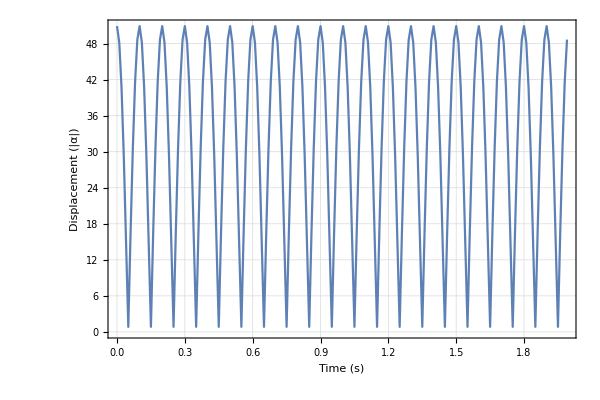
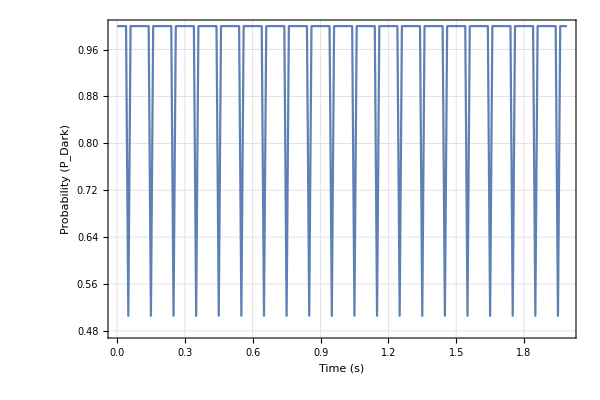
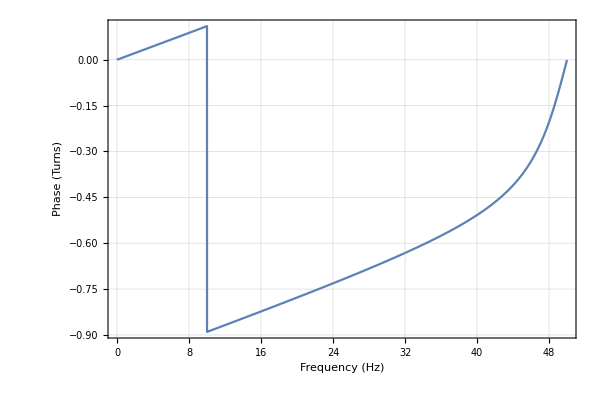
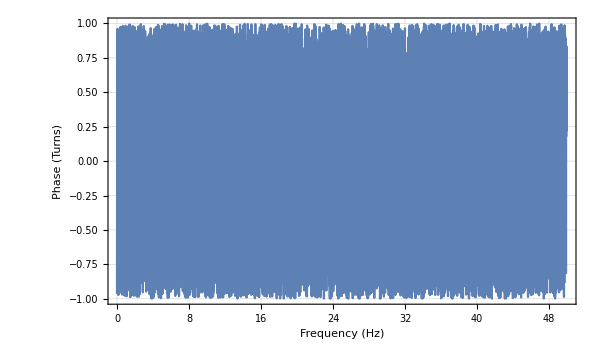
{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

```mathematica
resSummaryDJ={
plotDisplacementResults,
{plotPhononFFTMag,plotPhononFFTPhase},
{plotDataFFTMag,plotDataFFTPhase}
}
(*plotDataFFTMag*)
```

# Averaging - Test

```mathematica
(*set number of averaging trials*)
numTrials=1.*^4;
```

## Setup

```mathematica
tmpFuncAvg[probArr_]:=With[
{
yz0=FastBernoulliRandom[probArr]
},
Return[
Max[Abs[
Fourier[
yz0-Mean[yz0],
FourierParameters->{1,-1}
][[;;IntegerPart[numSamplePoints/2.]]]
]]^2.
]
];
```

```mathematica
RepeatedTiming[
tmpFuncAvg[probSampledArr];,
2.
]
```

{0.00820701,Null}

## Run Averaging

```mathematica
(*do multiple trials*)
avgRunTime=First@AbsoluteTiming[
resAvgArr=ParallelMap[
tmpFuncAvg[probSampledArr]&,
Range[numTrials]
];
]
```

18.9787

```mathematica
(*process results - signal*)
avgDistFit=EstimatedDistribution[resAvgArr,NormalDistribution[μ,σ]];
(*avgDistributionFit=EstimatedDistribution[resAvgArr,GammaDistribution[α,β]]*)
avgHistBinSize=Mean[#[[2;;-1]]-#[[1;;-2]]]&[HistogramList[resAvgArr,"Wand","Probability"][[1]]];
```

```mathematica
(*format results*)
avgHistPlot=Histogram[
resAvgArr,
"Wand","Probability",

FrameLabel->{
 {Style["Probability",{Black,Directive[15]}],None},
{
Style["Peak Power (Ampl^(2  .10))",{Black,Directive[15]}],
Style["Corr. Samp. (Sim): Peak Pow. Stats - N = "<>ToString[numTrials]<>" Trials",{Black,Directive[15]}]
}
},
ImageSize->Scaled[0.4],
PerformanceGoal->"Speed"
];
avgDistFitPlot=Plot[
avgHistBinSize*PDF[avgDistFit,x],
{x,#1,#2},

ImageSize->Scaled[0.4],
PerformanceGoal->"Speed"
]&[
Mean[avgDistFit]-5.*StandardDeviation[avgDistFit],
Mean[avgDistFit]+5.*StandardDeviation[avgDistFit]
];
```

## Do Background (from Main dataset only; single run)

```mathematica
(*remove peak points to make hist happier*)
bgrPoints=dataFFTMag[[;;,2]];
(*bgrThreshold=1.*^-1*Max[bgrPoints];*)
bgrThreshold=Mean[bgrPoints]+StandardDeviation[bgrPoints]*4.;
AbsoluteTiming[
bgrPointsReduced=Select[bgrPoints,#<bgrThreshold&];
]
Length/@{bgrPoints,bgrPointsReduced}
```

{0.006804,Null}

{{12500},{12494}}

## Do

```mathematica
(*process results - background*)
bgrDistFit=EstimatedDistribution[bgrPointsReduced,GammaDistribution[α,β]];
bgrHistBinSize=Mean[#[[2;;-1]]-#[[1;;-2]]]&[HistogramList[bgrPointsReduced,"Scott","Probability"][[1]]];
```

```mathematica
(*format results*)
bgrHistPlot=Histogram[
bgrPointsReduced,
"Scott",
"Probability",

FrameLabel->{
 {Style["Probability",{Black,Directive[15]}],None},
{
Style["Bgr. Power (Ampl^2)",{Black,Directive[15]}],
Style["CorrSamp (Sim): Bgr. Pow. Stats - N = "<>ToString[numSamplePoints]<>" Samples",{Black,Directive[15]}]
}
},
ImageSize->Scaled[0.4],
PerformanceGoal->"Speed"
];
```

```mathematica
bgrDistFitPlot=Plot[
bgrHistBinSize*PDF[bgrDistFit,x],
{x,#1,#2},

ImageSize->Scaled[0.4],
PerformanceGoal->"Speed"
]&[
0.(*Mean[bgrDistFit]-5.*StandardDeviation[bgrDistFit]*),
Mean[bgrDistFit]+5.*StandardDeviation[bgrDistFit]
];
```

# Averaging - Show

{(18.9787),(<|δ→6314.6,α→{20.,20.},ϕ→{0.,π}|>
<|δ→6251.77,α→{20.,20.},ϕ→{0.,π}|>),(250.
0.01
25001)}

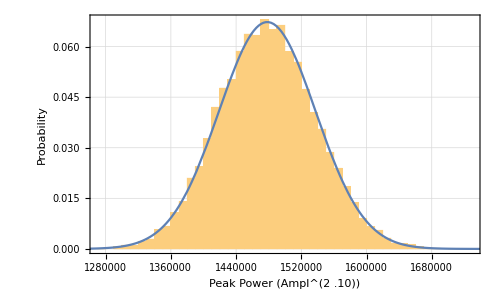
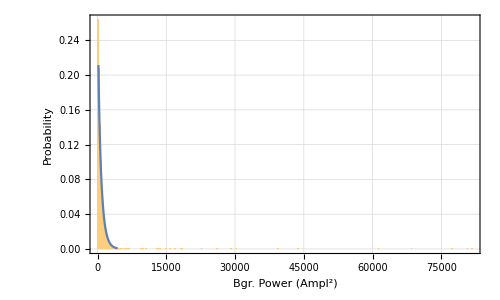
((NormalDistribution[1.47825×10^6,59306.6]
1.47825×10^6
59306.6
-Graphics-)
(GammaDistribution[0.891253,782.118]
697.066
738.368
-Graphics-)
-Graphics-)

```mathematica
(*show!*)
MatrixForm/@{{avgRunTime},toneConfig,{sampleTimeSec,samplePeriod,numSamplePoints}}
{
Transpose[{
avgDistFit,
Mean[avgDistFit],
StandardDeviation[avgDistFit],
Show[{avgHistPlot,avgDistFitPlot},ImageSize->{500,300},AspectRatio->Full]
}]//MatrixForm,
Transpose[{
bgrDistFit,
Mean[bgrDistFit],
StandardDeviation[bgrDistFit],
Show[{bgrHistPlot,bgrDistFitPlot},PlotRange->Automatic,ImageSize->{500,300},AspectRatio->Full]
}]//MatrixForm,
Show[plotDataFFTMag,ImageSize->{500,300},AspectRatio->Full]
}//MatrixForm
```

# Deprecated

## Fast Averaging

```mathematica
(*
(*use vectorization of randominteger by batching calls - kinda like compression*)
Length[probSampledArr]
DeleteDuplicates[probSampledArr]//Length
DeleteDuplicates[Round[probSampledArr,1.*^-5]]//Length

kk0=Round[probSampledArr,1.*^-8];
kk1=DeleteDuplicates[kk0];
kk2=Tally[kk0];*)
```

```mathematica
(*(*first test - naive*)
kkc=BernoulliDistribution[#]&/@probSampledArr;
AbsoluteTiming[
th0=RandomInteger/@kkc;
th1=Fourier[
th0-Mean[th0],
FourierParameters->{1,-1}
][[;;IntegerPart[numSamplePoints/2.]]];
th2=Max[Abs[th1]]^2.
]*)
```